```mathematica
SetDirectory["/Users/vsvh/docs/research/comm_patterns_git"]
```

/Users/vsvh/docs/research/comm_patterns_git

{{0,1,1.},{0,2,1.},{0,3,1.},{0,4,0.852853},{0,5,0.732733},{0,6,0.627628},{0,7,0.593093},{0,8,0.551051},{0,9,0.512012},{0,10,0.484985},{0,11,0.447447},{0,12,0.415916},{0,13,0.373874},{0,14,0.331832},{0,15,0.282282},{0,16,0.216216},{0,17,0.159159},{0,18,0.112613},{0,19,0.0675676},{0,20,0.00750751},{1,1,1.},{1,2,1.},{1,3,1.},{1,4,0.928017},{1,5,0.837685},{1,6,0.745236},{1,7,0.712773},{1,8,0.675371},{1,9,0.654199},{1,10,0.608327},{1,11,0.583627},{1,12,0.538462},{1,13,0.460833},{1,14,0.396613},{1,15,0.331687},{1,16,0.249118},{1,17,0.1729},{1,18,0.122089},{1,19,0.0677488},{1,20,0.00705716},{2,1,1.},{2,2,1.},{2,3,1.},{2,4,0.962299},{2,5,0.92046},{2,6,0.847356},{2,7,0.796322},{2,8,0.774253},{2,9,0.732874},{2,10,0.685517},{2,11,0.663448},{2,12,0.64092},{2,13,0.572874},{2,14,0.512644},{2,15,0.452414},{2,16,0.364138},{2,17,0.238621},{2,18,0.144368},{2,19,0.08},{2,20,0.0225287},{3,1,1.},{3,2,1.},{3,3,1.},{3,4,0.990722},{3,5,0.954124},{3,6,0.881443},{3,7,0.84433},{3,8,0.839691},{3,9,0.807732},{3,10,0.770619},{3,11,0.73866},{3,12,0.703093},{3,13,0.682474},{3,14,0.614433},{3,15,0.529381},{3,16,0.375773},{3,17,0.203608},{3,18,0.103608},{3,19,0.0649485},{3,20,0.00463918}}

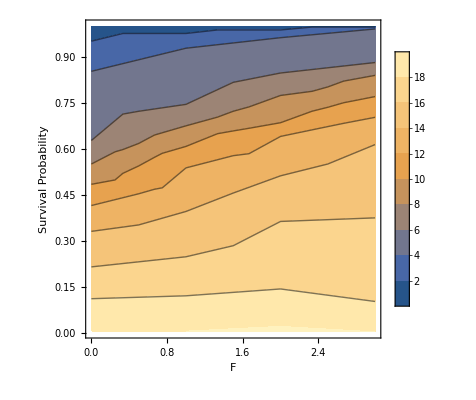

```mathematica
data = Import["/Users/vsvh/docs/research/commpatterns/data/contour.dat"]
```

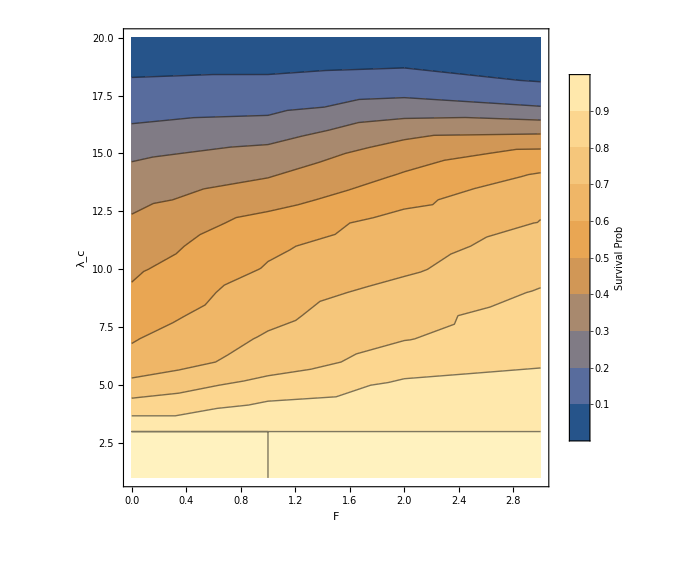

Thread::tdlen: Objects of unequal length in {{\"\<x\>\", \"\<y\>\", \"\<z\>\"}, {1, 1., 0}, {2, 1., 0}, {3, 1., 0}, {4, 0.852853, 0}, {5, 0.732733, 0}, {6, 0.627628, 0}, {7, 0.593093, 0}, {8, 0.551051, 0}, {9, 0.512012, 0}, «71»}\\\ {1} cannot be combined.

```mathematica
pc = ListContourPlot[data,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Survival Prob",LabelStyle->{ Italic,FontFamily->"Helvetica", FontSize->20}],Right], FrameLabel->{"F","\[\Lambda]_c"}, LabelStyle->{FontFamily->"Helvetica", FontSize->18}, ImageSize->Large]
```

```mathematica
Export["~/Desktop/contour.png", pc]
```

~/Desktop/contour.png